## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="PGK";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
Q10=2.5;


(* user will need to change this path *)
(*pathMASSef = "/Users/guest/Desktop/internship stuff/MASSef_1/";*)
pathMASSef = "C:/MASSef/";
kineticDataFileName =  "kinetic_data_MASSpy.csv";

mainFolder = "fit_PGK_MASSpy_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Molecule::shdw: Symbol Molecule appears in multiple contexts {AutomaticUnits`,System`}; definitions in context AutomaticUnits` may shadow or be shadowed by other definitions.

Working dir:C:\MASSef\examples\

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological, Q10];
```

((13dpg)^c+adp^c⇌(3pg)^c+atp^c)^PGK

random;

Structure:

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | Null | 1900 | 1805.
1995. | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | adp | 0.000085 | 0.00008075
0.00008925 |  | M | 7 | 25 |  | 
1 | 13dpg | 0.000011 | 0.00001045
0.00001155 |  | M | 7 | 25 |  | 
1 | atp | 0.0035 | 0.003325
0.003675 |  | M | 7 | 25 |  | 
1 | 3pg | 0.0025 | 0.002375
0.002625 |  | M | 7 | 25 |  |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | adp | Null
13dpg | Null | 2327.18 | 2210.82
2443.54 | 1/s | 7 | 37 |  | 
1 | 3pg | Null
atp | Null | 30.0281 | 28.5267
31.5295 | 1/s | 7 | 37 |  |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,1,1,1};
s05Priorities = Null;
kcatPriorities = {1,1};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

((13dpg)^c+adp^c⇌(3pg)^c+atp^c)^PGK

random;

Structure:

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | Null | 1900 | 1805.
1995. | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | adp | 0.000085 | 0.00008075
0.00008925 |  | M | 7 | 25 |  | 
1 | 13dpg | 0.000011 | 0.00001045
0.00001155 |  | M | 7 | 25 |  | 
1 | atp | 0.0035 | 0.003325
0.003675 |  | M | 7 | 25 |  | 
1 | 3pg | 0.0025 | 0.002375
0.002625 |  | M | 7 | 25 |  |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | adp | Null
13dpg | Null | 2327.18 | 2210.82
2443.54 | 1/s | 7 | 37 |  | 
1 | 3pg | Null
atp | Null | 30.0281 | 28.5267
31.5295 | 1/s | 7 | 37 |  |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_PGK[c] + 13dpg[c] <=> E_PGK[c]&13dpg",
				"E_PGK[c]&13dpg + adp[c] <=> E_PGK[c]&13dpg&adp",

				"E_PGK[c] + adp[c] <=> E_PGK[c]&adp",
				"E_PGK[c]&adp + 13dpg[c] <=> E_PGK[c]&13dpg&adp",

				"E_PGK[c]&13dpg&adp <=> E_PGK[c]&3pg&atp",

				"E_PGK[c]&3pg&atp <=> E_PGK[c]&3pg + atp[c]",
				"E_PGK[c]&3pg <=> E_PGK[c] + 3pg[c]",
				
				"E_PGK[c]&3pg&atp <=> E_PGK[c]&atp + 3pg[c]",
				"E_PGK[c]&atp <=> E_PGK[c] + atp[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((PGK^c)_^+adp^c⇌(PGK^c&adp^c)_^)^PGK1,((PGK^c)_^+(13dpg)^c⇌(PGK^c&(13dpg)^c)_^)^PGK2,((PGK^c&atp^c)_^⇌(PGK^c)_^+atp^c)^PGK3,((PGK^c&(3pg)^c)_^⇌(PGK^c)_^+(3pg)^c)^PGK4,((PGK^c&adp^c)_^+(13dpg)^c⇌(PGK^c&(13dpg)^c&adp^c)_^)^PGK5,((PGK^c&(13dpg)^c)_^+adp^c⇌(PGK^c&(13dpg)^c&adp^c)_^)^PGK6,((PGK^c&(3pg)^c&atp^c)_^⇌(PGK^c&atp^c)_^+(3pg)^c)^PGK7,((PGK^c&(3pg)^c&atp^c)_^⇌(PGK^c&(3pg)^c)_^+atp^c)^PGK8,((PGK^c&(13dpg)^c&adp^c)_^⇌(PGK^c&(3pg)^c&atp^c)_^)^PGK9}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((PGK^c)_^+adp^c⇌(PGK^c&adp^c)_^)^PGK1, ((PGK^c&adp^c)_^+(13dpg)^c⇌(PGK^c&(13dpg)^c&adp^c)_^)^PGK5, ((PGK^c&(13dpg)^c&adp^c)_^⇌(PGK^c&(3pg)^c&atp^c)_^)^PGK9, Overscript[(PGK^c&(3pg)^c&atp^c)_^⇌(PGK^c&(3pg)^c)_^+atp^c, PGK8], Overscript[(PGK^c&(3pg)^c)_^⇌(PGK^c)_^+(3pg)^c, PGK4]};
catalyticReactionsSet2={((PGK^c)_^+adp^c⇌(PGK^c&adp^c)_^)^PGK1, ((PGK^c&adp^c)_^+(13dpg)^c⇌(PGK^c&(13dpg)^c&adp^c)_^)^PGK5, ((PGK^c&(13dpg)^c&adp^c)_^⇌(PGK^c&(3pg)^c&atp^c)_^)^PGK9, Overscript[(PGK^c&(3pg)^c&atp^c)_^⇌(PGK^c&atp^c)_^+(3pg)^c, PGK7], Overscript[(PGK^c&atp^c)_^⇌(PGK^c)_^+atp^c, PGK3]};
catalyticReactionsSet3={((PGK^c)_^+(13dpg)^c⇌(PGK^c&(13dpg)^c)_^)^PGK2, ((PGK^c&(13dpg)^c)_^+adp^c⇌(PGK^c&(13dpg)^c&adp^c)_^)^PGK6, ((PGK^c&(13dpg)^c&adp^c)_^⇌(PGK^c&(3pg)^c&atp^c)_^)^PGK9,  Overscript[(PGK^c&(3pg)^c&atp^c)_^⇌(PGK^c&(3pg)^c)_^+atp^c, PGK8], Overscript[(PGK^c&(3pg)^c)_^⇌(PGK^c)_^+(3pg)^c, PGK4]};
catalyticReactionsSet4={((PGK^c)_^+(13dpg)^c⇌(PGK^c&(13dpg)^c)_^)^PGK2, ((PGK^c&(13dpg)^c)_^+adp^c⇌(PGK^c&(13dpg)^c&adp^c)_^)^PGK6, ((PGK^c&(13dpg)^c&adp^c)_^⇌(PGK^c&(3pg)^c&atp^c)_^)^PGK9, Overscript[(PGK^c&(3pg)^c&atp^c)_^⇌(PGK^c&atp^c)_^+(3pg)^c, PGK7], Overscript[(PGK^c&atp^c)_^⇌(PGK^c)_^+atp^c, PGK3]};
catalyticReactionsSetsList = {catalyticReactionsSet1, catalyticReactionsSet2, catalyticReactionsSet3, catalyticReactionsSet4};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=1;
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={};
otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList, inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

Added inhibition reactions:

{}

Generating flux equation...

{((PGK^c&(13dpg)^c&adp^c)_^-((PGK^c&(3pg)^c&atp^c)_^)/K_PGK9) Volume_c k_PGK9^⟶}

Volume_c (-(PGK^c&(3pg)^c&atp^c)_^ k_PGK9^⟵+(PGK^c&(13dpg)^c&adp^c)_^ k_PGK9^⟶)

Simplifying...

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

```mathematica
FilePrint@dataPathList
```

Priority	13dpg[c]	adp[c]	atp[c]	3pg[c]	param_PGK_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_1.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_1.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_1.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_1.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_1.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_1.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_1.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_1.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_1.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_1.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_1.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_2.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_2.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_2.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_2.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_2.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_2.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_2.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_2.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_2.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_2.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_2.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_3.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_3.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_3.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_3.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_3.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_3.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_3.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_3.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_3.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_3.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_3.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_4.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_4.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_4.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_4.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_4.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_4.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_4.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_4.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_4.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_4.txt"	1900
1	0	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\haldaneRatio_4.txt"	1900
1	1	8.500000000000002e-6	0	0	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateFor_adp.txt"	0.09090909090909091
1	1	0.000013471592135919474	0	0	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateFor_adp.txt"	0.13680688860321008
1	1	0.000021351034667831454	0	0	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateFor_adp.txt"	0.20076000891310192
1	1	0.000033839109497047245	0	0	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateFor_adp.txt"	0.2847472489508013
1	1	0.00005363137428081642	0	0	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateFor_adp.txt"	0.3868631798468569
1	1	0.00008500000000000002	0	0	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateFor_adp.txt"	0.5000000000000001
1	1	0.00013471592135919474	0	0	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateFor_adp.txt"	0.6131368201531432
1	1	0.00021351034667831454	0	0	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateFor_adp.txt"	0.7152527510491988
1	1	0.00033839109497047284	0	0	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateFor_adp.txt"	0.7992399910868982
1	1	0.0005363137428081642	0	0	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateFor_adp.txt"	0.86319311139679
1	1	0.0008500000000000003	0	0	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateFor_adp.txt"	0.9090909090909092
1	1.100000000000001e-6	1	0	0	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateFor_13dpg.txt"	0.09090909090909097
1	1.7433825117072269e-6	1	0	0	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateFor_13dpg.txt"	0.13680688860321014
1	2.7630750746605424e-6	1	0	0	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateFor_13dpg.txt"	0.200760008913102
1	4.37917887608847e-6	1	0	0	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateFor_13dpg.txt"	0.2847472489508014
1	6.940530789282128e-6	1	0	0	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateFor_13dpg.txt"	0.38686317984685703
1	0.000011000000000000008	1	0	0	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateFor_13dpg.txt"	0.5000000000000002
1	0.00001743382511707227	1	0	0	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateFor_13dpg.txt"	0.6131368201531434
1	0.000027630750746605424	1	0	0	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateFor_13dpg.txt"	0.7152527510491988
1	0.00004379178876088469	1	0	0	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateFor_13dpg.txt"	0.7992399910868982
1	0.00006940530789282128	1	0	0	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateFor_13dpg.txt"	0.8631931113967901
1	0.00011000000000000009	1	0	0	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateFor_13dpg.txt"	0.9090909090909092
1	0	0	0.00035000000000000005	1	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateRev_atp.txt"	0.09090909090909091
1	0	0	0.0005547126173613899	1	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateRev_atp.txt"	0.13680688860321005
1	0	0	0.000879160251028353	1	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateRev_atp.txt"	0.20076000891310175
1	0	0	0.0013933750969372409	1	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateRev_atp.txt"	0.28474724895080145
1	0	0	0.0022083507056806758	1	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateRev_atp.txt"	0.38686317984685686
1	0	0	0.0035	1	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateRev_atp.txt"	0.5
1	0	0	0.0055471261736139	1	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateRev_atp.txt"	0.6131368201531431
1	0	0	0.008791602510283538	1	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateRev_atp.txt"	0.7152527510491987
1	0	0	0.013933750969372407	1	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateRev_atp.txt"	0.7992399910868984
1	0	0	0.022083507056806766	1	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateRev_atp.txt"	0.8631931113967901
1	0	0	0.035	1	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateRev_atp.txt"	0.9090909090909091
1	0	0	1	0.00024999999999999995	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateRev_3pg.txt"	0.0909090909090909
1	0	0	1	0.0003962232981152784	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateRev_3pg.txt"	0.13680688860321003
1	0	0	1	0.0006279716078773948	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateRev_3pg.txt"	0.20076000891310167
1	0	0	1	0.0009952679263837431	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateRev_3pg.txt"	0.2847472489508014
1	0	0	1	0.0015773933612004821	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateRev_3pg.txt"	0.3868631798468568
1	0	0	1	0.002499999999999999	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateRev_3pg.txt"	0.4999999999999999
1	0	0	1	0.0039622329811527844	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateRev_3pg.txt"	0.6131368201531431
1	0	0	1	0.006279716078773954	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateRev_3pg.txt"	0.7152527510491987
1	0	0	1	0.00995267926383743	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateRev_3pg.txt"	0.7992399910868982
1	0	0	1	0.01577393361200483	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateRev_3pg.txt"	0.8631931113967901
1	0	0	1	0.024999999999999994	1	7	25	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\relRateRev_3pg.txt"	0.9090909090909092
1	1	1	0	0	1	7	37	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\absRateFor.txt"	2327.1785908390234
1	1	1	0	0	1	7	37	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\absRateFor.txt"	2327.1785908390234
1	1	1	0	0	1	7	37	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\absRateFor.txt"	2327.1785908390234
1	1	1	0	0	1	7	37	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\absRateFor.txt"	2327.1785908390234
1	1	1	0	0	1	7	37	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\absRateFor.txt"	2327.1785908390234
1	1	1	0	0	1	7	37	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\absRateFor.txt"	2327.1785908390234
1	1	1	0	0	1	7	37	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\absRateFor.txt"	2327.1785908390234
1	1	1	0	0	1	7	37	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\absRateFor.txt"	2327.1785908390234
1	1	1	0	0	1	7	37	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\absRateFor.txt"	2327.1785908390234
1	1	1	0	0	1	7	37	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\absRateFor.txt"	2327.1785908390234
1	1	1	0	0	1	7	37	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\absRateFor.txt"	2327.1785908390234
1	0	0	1	1	1	7	37	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	0	0	1	1	1	7	37	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	0	0	1	1	1	7	37	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	0	0	1	1	1	7	37	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	0	0	1	1	1	7	37	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	0	0	1	1	1	7	37	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	0	0	1	1	1	7	37	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	0	0	1	1	1	7	37	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	0	0	1	1	1	7	37	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	0	0	1	1	1	7	37	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786
1	0	0	1	1	1	7	37	"C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\absRateRev.txt"	30.028110849535786

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.1368068886032101
1	0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310197
1	0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.2847472489508014
1	0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.38686317984685703
1	0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000001
1	0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491988
1	0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909091
1	0	0.0001345263278918314	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.09090909090909088
1	0	0.0002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.13680688860321
1	0	0.00033791485771230003	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.20076000891310167
1	0	0.0005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508014
1	0	0.0008488037460930167	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468568
1	0	0.0013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.49999999999999994
1	0	0.002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.613136820153143
1	0	0.0033791485771230037	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491987
1	0	0.005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868981
1	0	0.008488037460930166	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.8631931113967899
1	0	0.013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.909090909090909
1	0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.0909090909090909
1	0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321005
1	0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310167
1	0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508014
1	0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468568
1	0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491987
1	0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.86319311139679
1	0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909091
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909093
1	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.090909090909091
1	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.1368068886032102
1	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2007600089131019
1	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508017
1	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468571
1	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.5000000000000003
1	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.6131368201531434
1	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491988
1	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868984
1	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.86319311139679
1	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909092
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=10;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	10
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	18
filesWithFunctions	[C:\\MASSef\\examples\\fit_PGK_MASSpy_typeII\\input\\absRateFor.txt, C:\\MASSef\\examples\\fit_PGK_MASSpy_typeII\\input\\absRateRev.txt, C:\\MASSef\\examples\\fit_PGK_MASSpy_typeII\\input\\relRateFor_13dpg.txt, C:\\MASSef\\examples\\fit_PGK_MASSpy_typeII\\input\\relRateFor_adp.txt, C:\\MASSef\\examples\\fit_PGK_MASSpy_typeII\\input\\relRateRev_3pg.txt, C:\\MASSef\\examples\\fit_PGK_MASSpy_typeII\\input\\relRateRev_atp.txt, C:\\MASSef\\examples\\fit_PGK_MASSpy_typeII\\input\\haldaneRatio_1.txt, C:\\MASSef\\examples\\fit_PGK_MASSpy_typeII\\input\\haldaneRatio_2.txt, C:\\MASSef\\examples\\fit_PGK_MASSpy_typeII\\input\\haldaneRatio_3.txt, C:\\MASSef\\examples\\fit_PGK_MASSpy_typeII\\input\\haldaneRatio_4.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	18
filesWithFunctions	[C:\\MASSef\\examples\\fit_PGK_typeII\\input\\absRateFor.txt, C:\\MASSef\\examples\\fit_PGK_typeII\\input\\absRateRev.txt, C:\\MASSef\\examples\\fit_PGK_typeII\\input\\relRateFor_13dpg.txt, C:\\MASSef\\examples\\fit_PGK_typeII\\input\\relRateFor_adp.txt, C:\\MASSef\\examples\\fit_PGK_typeII\\input\\relRateRev_3pg.txt, C:\\MASSef\\examples\\fit_PGK_typeII\\input\\relRateRev_atp.txt, C:\\MASSef\\examples\\fit_PGK_typeII\\input\\haldaneRatio_1.txt, C:\\MASSef\\examples\\fit_PGK_typeII\\input\\haldaneRatio_2.txt, C:\\MASSef\\examples\\fit_PGK_typeII\\input\\haldaneRatio_3.txt, C:\\MASSef\\examples\\fit_PGK_typeII\\input\\haldaneRatio_4.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 3.193072492364541
best_fit: 3.0314151648186707
best_fit: 4.373368306801649
best_fit: 1.0020549216319126
best_fit: 4.142863862031001
best_fit: 10.356219492968176
best_fit: 1.007337939272406
best_fit: 5.6715488260822955
best_fit: 1.0984066673092516
best_fit: 1.6099790033747692

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

Part::partd: Part specification C:\MASSef\examples\fit_PGK_MASSpy_typeII\input\PGK_PGK.dat⟦2⟧ is longer than depth of object.

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 1.60309×10^-6 | 2.56989×10^-12 | 0.00701339 | 0.000369126 | 1900 | 1900.01
1 | haldaneRatio_1 | 1.60309×10^-6 | 2.56989×10^-12 | 0.00701339 | 0.000369126 | 1900 | 1900.01
1 | haldaneRatio_1 | 1.60309×10^-6 | 2.56989×10^-12 | 0.00701339 | 0.000369126 | 1900 | 1900.01
1 | haldaneRatio_1 | 1.60309×10^-6 | 2.56989×10^-12 | 0.00701339 | 0.000369126 | 1900 | 1900.01
1 | haldaneRatio_1 | 1.60309×10^-6 | 2.56989×10^-12 | 0.00701339 | 0.000369126 | 1900 | 1900.01
1 | haldaneRatio_1 | 1.60309×10^-6 | 2.56989×10^-12 | 0.00701339 | 0.000369126 | 1900 | 1900.01
1 | haldaneRatio_1 | 1.60309×10^-6 | 2.56989×10^-12 | 0.00701339 | 0.000369126 | 1900 | 1900.01
1 | haldaneRatio_1 | 1.60309×10^-6 | 2.56989×10^-12 | 0.00701339 | 0.000369126 | 1900 | 1900.01
1 | haldaneRatio_1 | 1.60309×10^-6 | 2.56989×10^-12 | 0.00701339 | 0.000369126 | 1900 | 1900.01
1 | haldaneRatio_1 | 1.60309×10^-6 | 2.56989×10^-12 | 0.00701339 | 0.000369126 | 1900 | 1900.01
1 | haldaneRatio_1 | 1.60309×10^-6 | 2.56989×10^-12 | 0.00701339 | 0.000369126 | 1900 | 1900.01
1 | haldaneRatio_2 | 0.0000107527 | 1.15619×10^-10 | 0.0470425 | 0.00247592 | 1900 | 1900.05
1 | haldaneRatio_2 | 0.0000107527 | 1.15619×10^-10 | 0.0470425 | 0.00247592 | 1900 | 1900.05
1 | haldaneRatio_2 | 0.0000107527 | 1.15619×10^-10 | 0.0470425 | 0.00247592 | 1900 | 1900.05
1 | haldaneRatio_2 | 0.0000107527 | 1.15619×10^-10 | 0.0470425 | 0.00247592 | 1900 | 1900.05
1 | haldaneRatio_2 | 0.0000107527 | 1.15619×10^-10 | 0.0470425 | 0.00247592 | 1900 | 1900.05
1 | haldaneRatio_2 | 0.0000107527 | 1.15619×10^-10 | 0.0470425 | 0.00247592 | 1900 | 1900.05
1 | haldaneRatio_2 | 0.0000107527 | 1.15619×10^-10 | 0.0470425 | 0.00247592 | 1900 | 1900.05
1 | haldaneRatio_2 | 0.0000107527 | 1.15619×10^-10 | 0.0470425 | 0.00247592 | 1900 | 1900.05
1 | haldaneRatio_2 | 0.0000107527 | 1.15619×10^-10 | 0.0470425 | 0.00247592 | 1900 | 1900.05
1 | haldaneRatio_2 | 0.0000107527 | 1.15619×10^-10 | 0.0470425 | 0.00247592 | 1900 | 1900.05
1 | haldaneRatio_2 | 0.0000107527 | 1.15619×10^-10 | 0.0470425 | 0.00247592 | 1900 | 1900.05
1 | haldaneRatio_3 | 2.58016×10^-6 | 6.65721×10^-12 | 0.0112879 | 0.000594101 | 1900 | 1899.99
1 | haldaneRatio_3 | 2.58016×10^-6 | 6.65721×10^-12 | 0.0112879 | 0.000594101 | 1900 | 1899.99
1 | haldaneRatio_3 | 2.58016×10^-6 | 6.65721×10^-12 | 0.0112879 | 0.000594101 | 1900 | 1899.99
1 | haldaneRatio_3 | 2.58016×10^-6 | 6.65721×10^-12 | 0.0112879 | 0.000594101 | 1900 | 1899.99
1 | haldaneRatio_3 | 2.58016×10^-6 | 6.65721×10^-12 | 0.0112879 | 0.000594101 | 1900 | 1899.99
1 | haldaneRatio_3 | 2.58016×10^-6 | 6.65721×10^-12 | 0.0112879 | 0.000594101 | 1900 | 1899.99
1 | haldaneRatio_3 | 2.58016×10^-6 | 6.65721×10^-12 | 0.0112879 | 0.000594101 | 1900 | 1899.99
1 | haldaneRatio_3 | 2.58016×10^-6 | 6.65721×10^-12 | 0.0112879 | 0.000594101 | 1900 | 1899.99
1 | haldaneRatio_3 | 2.58016×10^-6 | 6.65721×10^-12 | 0.0112879 | 0.000594101 | 1900 | 1899.99
1 | haldaneRatio_3 | 2.58016×10^-6 | 6.65721×10^-12 | 0.0112879 | 0.000594101 | 1900 | 1899.99
1 | haldaneRatio_3 | 2.58016×10^-6 | 6.65721×10^-12 | 0.0112879 | 0.000594101 | 1900 | 1899.99
1 | haldaneRatio_4 | 6.5694×10^-6 | 4.31571×10^-11 | 0.0287408 | 0.00151267 | 1900 | 1900.03
1 | haldaneRatio_4 | 6.5694×10^-6 | 4.31571×10^-11 | 0.0287408 | 0.00151267 | 1900 | 1900.03
1 | haldaneRatio_4 | 6.5694×10^-6 | 4.31571×10^-11 | 0.0287408 | 0.00151267 | 1900 | 1900.03
1 | haldaneRatio_4 | 6.5694×10^-6 | 4.31571×10^-11 | 0.0287408 | 0.00151267 | 1900 | 1900.03
1 | haldaneRatio_4 | 6.5694×10^-6 | 4.31571×10^-11 | 0.0287408 | 0.00151267 | 1900 | 1900.03
1 | haldaneRatio_4 | 6.5694×10^-6 | 4.31571×10^-11 | 0.0287408 | 0.00151267 | 1900 | 1900.03
1 | haldaneRatio_4 | 6.5694×10^-6 | 4.31571×10^-11 | 0.0287408 | 0.00151267 | 1900 | 1900.03
1 | haldaneRatio_4 | 6.5694×10^-6 | 4.31571×10^-11 | 0.0287408 | 0.00151267 | 1900 | 1900.03
1 | haldaneRatio_4 | 6.5694×10^-6 | 4.31571×10^-11 | 0.0287408 | 0.00151267 | 1900 | 1900.03
1 | haldaneRatio_4 | 6.5694×10^-6 | 4.31571×10^-11 | 0.0287408 | 0.00151267 | 1900 | 1900.03
1 | haldaneRatio_4 | 6.5694×10^-6 | 4.31571×10^-11 | 0.0287408 | 0.00151267 | 1900 | 1900.03
1 | relRateFor_adp | 0.0000102446 | 1.04952×10^-10 | 2.14443×10^-6 | 0.00235888 | 0.0909091 | 0.0909069
1 | relRateFor_adp | 7.8636×10^-6 | 6.18362×10^-11 | 2.47709×10^-6 | 0.00181064 | 0.136807 | 0.136804
1 | relRateFor_adp | 4.54594×10^-6 | 2.06656×10^-11 | 2.10143×10^-6 | 0.00104674 | 0.20076 | 0.200758
1 | relRateFor_adp | 1.88949×10^-7 | 3.57018×10^-14 | 1.23885×10^-7 | 0.0000435072 | 0.284747 | 0.284747
1 | relRateFor_adp | 5.10856×10^-6 | 2.60974×10^-11 | 4.55066×10^-6 | 0.0011763 | 0.386863 | 0.386868
1 | relRateFor_adp | 0.0000109779 | 1.20514×10^-10 | 0.0000126389 | 0.00252778 | 0.5 | 0.500013
1 | relRateFor_adp | 0.0000168473 | 2.83831×10^-10 | 0.0000237855 | 0.00387931 | 0.613137 | 0.613161
1 | relRateFor_adp | 0.000022145 | 4.90401×10^-10 | 0.0000364722 | 0.0050992 | 0.715253 | 0.715289
1 | relRateFor_adp | 0.0000265023 | 7.0237×10^-10 | 0.0000487741 | 0.00610256 | 0.79924 | 0.799289
1 | relRateFor_adp | 0.0000298202 | 8.89243×10^-10 | 0.0000592719 | 0.00686659 | 0.863193 | 0.863252
1 | relRateFor_adp | 0.0000322014 | 1.03693×10^-9 | 0.0000674084 | 0.00741492 | 0.909091 | 0.909158
1 | relRateFor_13dpg | 3.27902×10^-6 | 1.0752×10^-11 | 6.86381×10^-7 | 0.000755019 | 0.0909091 | 0.0909084
1 | relRateFor_13dpg | 2.87203×10^-6 | 8.24855×10^-12 | 9.04713×10^-7 | 0.000661307 | 0.136807 | 0.136806
1 | relRateFor_13dpg | 2.30494×10^-6 | 5.31273×10^-12 | 1.06549×10^-6 | 0.00053073 | 0.20076 | 0.200759
1 | relRateFor_13dpg | 1.56019×10^-6 | 2.4342×10^-12 | 1.02295×10^-6 | 0.000359247 | 0.284747 | 0.284746
1 | relRateFor_13dpg | 6.54693×10^-7 | 4.28623×10^-13 | 5.83191×10^-7 | 0.000150749 | 0.386863 | 0.386863
1 | relRateFor_13dpg | 3.48534×10^-7 | 1.21476×10^-13 | 4.01265×10^-7 | 0.0000802529 | 0.5 | 0.5
1 | relRateFor_13dpg | 1.35176×10^-6 | 1.82726×10^-12 | 1.90842×10^-6 | 0.000311255 | 0.613137 | 0.613139
1 | relRateFor_13dpg | 2.25727×10^-6 | 5.09526×10^-12 | 3.71757×10^-6 | 0.000519757 | 0.715253 | 0.715256
1 | relRateFor_13dpg | 3.00202×10^-6 | 9.01212×10^-12 | 5.52469×10^-6 | 0.000691243 | 0.79924 | 0.799246
1 | relRateFor_13dpg | 3.56912×10^-6 | 1.27386×10^-11 | 7.09393×10^-6 | 0.000821824 | 0.863193 | 0.8632
1 | relRateFor_13dpg | 3.97612×10^-6 | 1.58095×10^-11 | 8.32308×10^-6 | 0.000915539 | 0.909091 | 0.909099
1 | relRateRev_atp | 0.000563502 | 3.17535×10^-7 | 0.000117879 | 0.129667 | 0.0909091 | 0.0907912
1 | relRateRev_atp | 0.000458279 | 2.10019×10^-7 | 0.000144286 | 0.105467 | 0.136807 | 0.136663
1 | relRateRev_atp | 0.000311619 | 9.71067×10^-8 | 0.000144 | 0.0717273 | 0.20076 | 0.200616
1 | relRateRev_atp | 0.000118942 | 1.41472×10^-8 | 0.0000779743 | 0.0273837 | 0.284747 | 0.284669
1 | relRateRev_atp | 0.00011544 | 1.33264×10^-8 | 0.000102846 | 0.0265845 | 0.386863 | 0.386966
1 | relRateRev_atp | 0.000375265 | 1.40824×10^-7 | 0.000432227 | 0.0864454 | 0.5 | 0.500432
1 | relRateRev_atp | 0.000635246 | 4.03538×10^-7 | 0.000897497 | 0.146378 | 0.613137 | 0.614034
1 | relRateRev_atp | 0.000870036 | 7.56962×10^-7 | 0.00143432 | 0.200534 | 0.715253 | 0.716687
1 | relRateRev_atp | 0.00106324 | 1.13048×10^-6 | 0.00195909 | 0.24512 | 0.79924 | 0.801199
1 | relRateRev_atp | 0.00121041 | 1.4651×10^-6 | 0.00240914 | 0.279096 | 0.863193 | 0.865602
1 | relRateRev_atp | 0.00131607 | 1.73203×10^-6 | 0.00275905 | 0.303495 | 0.909091 | 0.91185
1 | relRateRev_3pg | 0.000490022 | 2.40122×10^-7 | 0.000102516 | 0.112768 | 0.0909091 | 0.0908066
1 | relRateRev_3pg | 0.000350745 | 1.23022×10^-7 | 0.000110443 | 0.0807294 | 0.136807 | 0.136696
1 | relRateRev_3pg | 0.000209209 | 4.37685×10^-8 | 0.0000966873 | 0.0481606 | 0.20076 | 0.200663
1 | relRateRev_3pg | 0.0000531675 | 2.82678×10^-9 | 0.0000348574 | 0.0122415 | 0.284747 | 0.284712
1 | relRateRev_3pg | 0.000120388 | 1.44932×10^-8 | 0.000107254 | 0.0277241 | 0.386863 | 0.38697
1 | relRateRev_3pg | 0.000304372 | 9.26425×10^-8 | 0.000350544 | 0.0701089 | 0.5 | 0.500351
1 | relRateRev_3pg | 0.000484334 | 2.3458×10^-7 | 0.000684165 | 0.111584 | 0.613137 | 0.613821
1 | relRateRev_3pg | 0.000644923 | 4.15926×10^-7 | 0.00106293 | 0.148609 | 0.715253 | 0.716316
1 | relRateRev_3pg | 0.000776198 | 6.02483×10^-7 | 0.00142973 | 0.178886 | 0.79924 | 0.80067
1 | relRateRev_3pg | 0.00087582 | 7.67061×10^-7 | 0.00174252 | 0.201869 | 0.863193 | 0.864936
1 | relRateRev_3pg | 0.000947178 | 8.97146×10^-7 | 0.00198485 | 0.218334 | 0.909091 | 0.911076
1 | absRateFor | 1.61107×10^-6 | 2.59554×10^-12 | 0.00863293 | 0.000370961 | 2327.18 | 2327.17
1 | absRateFor | 1.61107×10^-6 | 2.59554×10^-12 | 0.00863293 | 0.000370961 | 2327.18 | 2327.17
1 | absRateFor | 1.61107×10^-6 | 2.59554×10^-12 | 0.00863293 | 0.000370961 | 2327.18 | 2327.17
1 | absRateFor | 1.61107×10^-6 | 2.59554×10^-12 | 0.00863293 | 0.000370961 | 2327.18 | 2327.17
1 | absRateFor | 1.61107×10^-6 | 2.59554×10^-12 | 0.00863293 | 0.000370961 | 2327.18 | 2327.17
1 | absRateFor | 1.61107×10^-6 | 2.59554×10^-12 | 0.00863293 | 0.000370961 | 2327.18 | 2327.17
1 | absRateFor | 1.61107×10^-6 | 2.59554×10^-12 | 0.00863293 | 0.000370961 | 2327.18 | 2327.17
1 | absRateFor | 1.61107×10^-6 | 2.59554×10^-12 | 0.00863293 | 0.000370961 | 2327.18 | 2327.17
1 | absRateFor | 1.61107×10^-6 | 2.59554×10^-12 | 0.00863293 | 0.000370961 | 2327.18 | 2327.17
1 | absRateFor | 1.61107×10^-6 | 2.59554×10^-12 | 0.00863293 | 0.000370961 | 2327.18 | 2327.17
1 | absRateFor | 1.61107×10^-6 | 2.59554×10^-12 | 0.00863293 | 0.000370961 | 2327.18 | 2327.17
1 | absRateRev | 1.53498×10^-6 | 2.35616×10^-12 | 0.000106132 | 0.000353441 | 30.0281 | 30.028
1 | absRateRev | 1.53498×10^-6 | 2.35616×10^-12 | 0.000106132 | 0.000353441 | 30.0281 | 30.028
1 | absRateRev | 1.53498×10^-6 | 2.35616×10^-12 | 0.000106132 | 0.000353441 | 30.0281 | 30.028
1 | absRateRev | 1.53498×10^-6 | 2.35616×10^-12 | 0.000106132 | 0.000353441 | 30.0281 | 30.028
1 | absRateRev | 1.53498×10^-6 | 2.35616×10^-12 | 0.000106132 | 0.000353441 | 30.0281 | 30.028
1 | absRateRev | 1.53498×10^-6 | 2.35616×10^-12 | 0.000106132 | 0.000353441 | 30.0281 | 30.028
1 | absRateRev | 1.53498×10^-6 | 2.35616×10^-12 | 0.000106132 | 0.000353441 | 30.0281 | 30.028
1 | absRateRev | 1.53498×10^-6 | 2.35616×10^-12 | 0.000106132 | 0.000353441 | 30.0281 | 30.028
1 | absRateRev | 1.53498×10^-6 | 2.35616×10^-12 | 0.000106132 | 0.000353441 | 30.0281 | 30.028
1 | absRateRev | 1.53498×10^-6 | 2.35616×10^-12 | 0.000106132 | 0.000353441 | 30.0281 | 30.028
1 | absRateRev | 1.53498×10^-6 | 2.35616×10^-12 | 0.000106132 | 0.000353441 | 30.0281 | 30.028

### Simulated Data and Best Fit Data Plot

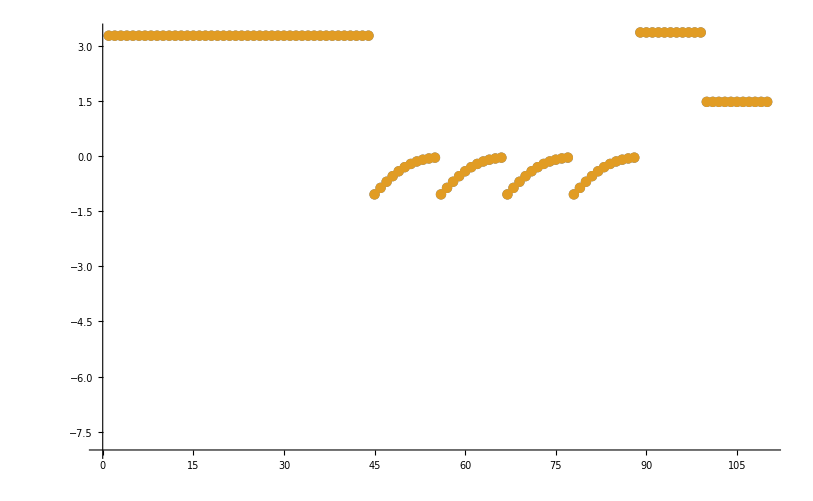

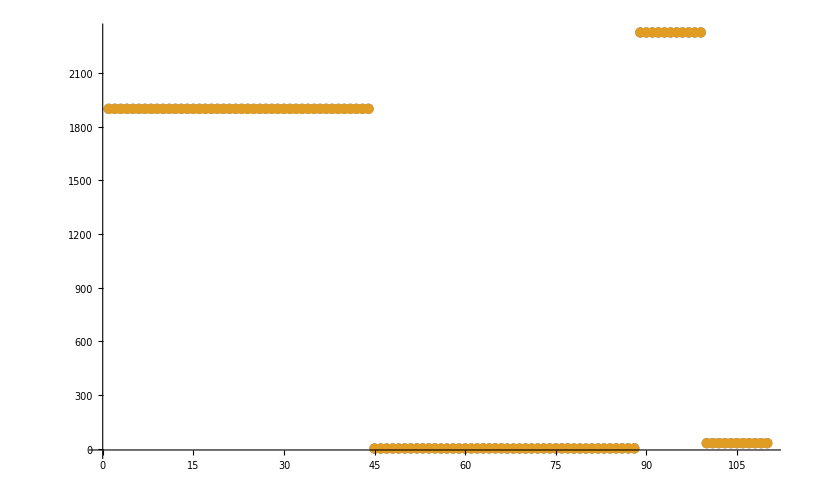

```mathematica
dataSetI=3;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

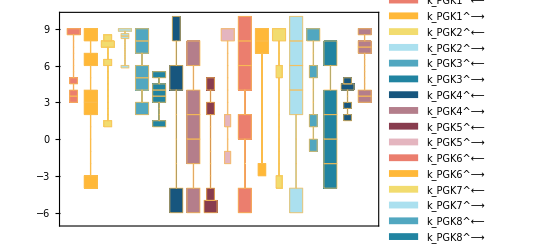

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[1;;5,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

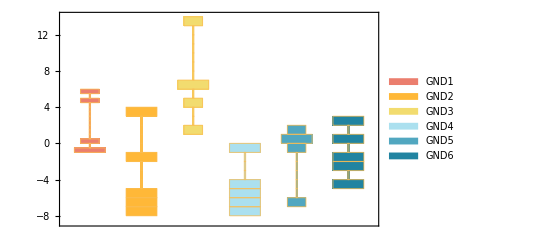

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

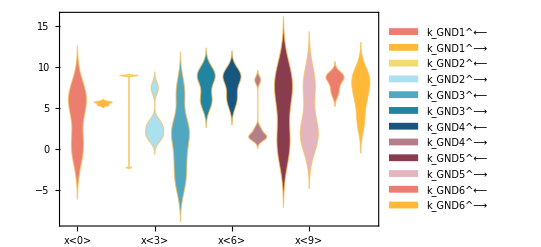

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

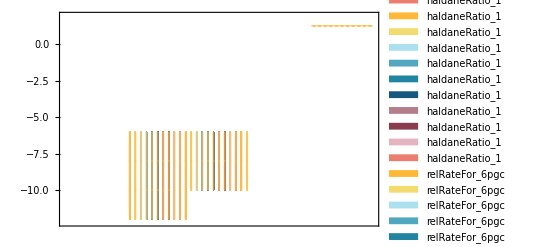

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

#### Cluster Parameters

```mathematica
(*clusters=FindClusters[Log10[filteredDataListRed[[All,2]]],Method->{"Agglomerate","Linkage"->"Complete","SignificanceTest"->{"Gap","Tolerance"->0.0001}}];(**)*)
clusters=FindClusters[Log10[filteredDataList[[1;;6,2]]],Method->{"Optimize","Iterations"->2}];
medianParamCluster=Table[Median[clusters[[cluster,All,param]]],{cluster,Length[clusters]},{param,Length[clusters[[1,1]]]}](*Switch to log space and use mean?*);
clusterSqdRes=Table[(clusters[[cluster,paramSet,param]]-medianParamCluster[[cluster,param]])^2,{cluster,Length[clusters]},{paramSet,Length[clusters[[cluster]]]},{param,Length[clusters[[1,1]]]}];
clusterSSE=Table[Total[clusterSqdRes[[cluster,paramSet]]],{cluster,Length[clusterSqdRes]},{paramSet,Length[clusterSqdRes[[cluster]]]}];
bestClusterSSE=Table[SortBy[clusterSSE[[cluster]],Less],{cluster,Length[clusterSSE]}][[All,1]];
finalClusterParams={};
Table[If[clusterSSE[[cluster,paramSet]]==bestClusterSSE[[cluster]],finalClusterParams=Append[finalClusterParams,clusters[[cluster,paramSet]]]],{cluster,Length[clusterSSE]},{paramSet,Length[clusterSSE[[cluster]]]}];
```

#### Print Representative Parameter Sets for Each Cluster (Optional)

```mathematica
TableForm[finalClusterParams]
```

8.99748 | 8.33165 | 3.65551 | 8.41034 | 9. | 6.17915 | 8.24867 | 5.54191 | -4.23708 | 5.0768 | 5.06688 | 8.96013 | 6.29732 | 3.81841 | -2.1041 | -4.69709 | 4.0749 | 4.00532

#### Parameter Cluster Plots (Optional)

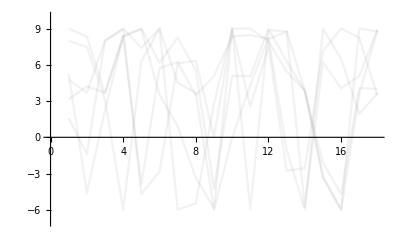

{-Graphics-}

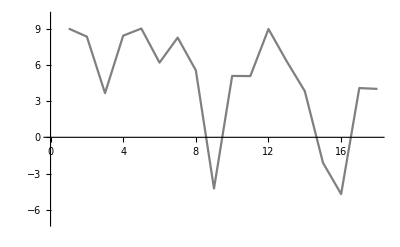

```mathematica
ListPlot[Log10[filteredDataList[[1;;6,2]]],"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[.1,Gray]](*All parameter sets*)
ListPlot[#,"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[.1,Gray]]&/@clusters
(*All parameter set clusters*)
ListPlot[#,"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[1,Gray]]&/@finalClusterParams(*Representative parameter sets*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=1;
paramSet = 1;
dataHeader = Import[dataFilePath][[1]];
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse,metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

data value | predicted value | error in %
0.000085 | 0.0000849964 | 0.00423497
0.000011 | 0.000011 | 0.000382447
0.0035 | 0.00349397 | 0.172288
0.0025 | 0.00249693 | 0.122993

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
2327.18 | 2327.18 | 0.0000555702

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1,3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
1900 | 1900. | 3.69725×10^-6

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
1900 | 1900. | 3.69725×10^-6

```mathematica
backCalculateKic[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

```mathematica
backCalculateKiu[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

#### Export rate back calculated parameter error distribution

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```

Set::shape: Lists {predictedParameters,predictedParameterErrors} and exportPredictedParametersAndErrors[((6pgc)^c+nadp^c⇌co2^c+nadph^c+ru5p__D^c)^GND,GND,«20»,{Priority,6pgc[c],co2[c],nadp[c],nadph[c],ru5p__D[c],param_GND_total,param_pH,param_Temp,FileFlag,Target_Data}] are not the same shape.

Part::take: Cannot take positions 3 through -1 in predictedParameterErrors.

Part::partd: Part specification predictedParameterErrors⟦1⟧ is longer than depth of object.

BoxWhiskerChart::ldata: Transpose[predictedParameterErrors⟦3;;All⟧] is not a valid dataset or list of datasets.

BoxWhiskerChart[Transpose[predictedParameterErrors⟦3;;All⟧],ChartLabels→{predictedParameterErrors⟦1⟧}]

## Export data

```mathematica
directoryExport = "C:\\Users\\Daniel Zielinski\\Desktop\\MASSpy Work\\"
CreateDirectory[directoryExport<>ToLowerCase[rxnName]]
indexLastGoodFit = 4;
```

C:\Users\Daniel Zielinski\Desktop\MASSpy Work\

CreateDirectory::filex: C:\Users\Daniel Zielinski\Desktop\MASSpy Work\pgk already exists.

$Failed

```mathematica
rateConstsString = ToString/@rateConstsSub[[All,1]];
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateconst_labels_"<>ToLowerCase[rxnName]<>".txt",rateConstsString]
```

C:\Users\Daniel Zielinski\Desktop\MASSpy Work\pgk\rateconst_labels_pgk.txt

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\S_"<>ToLowerCase[rxnName]<>".txt",S[enzymeModel]]
```

C:\Users\Daniel Zielinski\Desktop\MASSpy Work\pgk\S_pgk.txt

```mathematica
ToString/@getSpecies[enzymeModel]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\species_"<>ToLowerCase[rxnName]<>".txt",ToString/@getSpecies[enzymeModel]]
```

{E_PGK[c],E_PGK[c]&13dpg,E_PGK[c]&3pg,E_PGK[c]&adp,E_PGK[c]&atp,E_PGK[c]&13dpg&adp,13dpg[c],adp[c],atp[c],E_PGK[c]&3pg&atp,3pg[c]}

C:\Users\Daniel Zielinski\Desktop\MASSpy Work\pgk\species_pgk.txt

```mathematica
ToString/@getReactions[enzymeModel]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\reactions_"<>ToLowerCase[rxnName]<>".txt",ToString/@getReactions[enzymeModel]]
```

{PGK1: adp[c] + E_PGK[c] <=> E_PGK[c]&adp,PGK2: 13dpg[c] + E_PGK[c] <=> E_PGK[c]&13dpg,PGK3: E_PGK[c]&atp <=> atp[c] + E_PGK[c],PGK4: E_PGK[c]&3pg <=> 3pg[c] + E_PGK[c],PGK5: 13dpg[c] + E_PGK[c]&adp <=> E_PGK[c]&13dpg&adp,PGK6: adp[c] + E_PGK[c]&13dpg <=> E_PGK[c]&13dpg&adp,PGK7: E_PGK[c]&3pg&atp <=> 3pg[c] + E_PGK[c]&atp,PGK8: E_PGK[c]&3pg&atp <=> atp[c] + E_PGK[c]&3pg,PGK9: E_PGK[c]&13dpg&adp <=> E_PGK[c]&3pg&atp}

C:\Users\Daniel Zielinski\Desktop\MASSpy Work\pgk\reactions_pgk.txt

```mathematica
solEnz = Import["C:/MASSef/examples/"<>mainFolder <>"/input/enzSol_"<>rxnName<>"_.m"];
```

```mathematica
speciesStrings = ToString/@solEnz[[All,1]]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\equation_labels_"<>ToLowerCase[rxnName]<>".txt",ToString/@solEnz[[All,1]]];
```

{E_PGK[c],E_PGK[c]&13dpg,E_PGK[c]&3pg,E_PGK[c]&adp,E_PGK[c]&atp,E_PGK[c]&13dpg&adp,E_PGK[c]&3pg&atp}

```mathematica
pythonSubList = Thread[Variables[solEnz[[1,2]]]->(ToString/@Variables[solEnz[[1,2]]])];
ToPython[solEnz[[1,2]]/.pythonSubList]
Do[
Export[directoryExport <>ToLowerCase[rxnName]<>"\\equation_"<>speciesStrings[[i]]<>"_"<>ToLowerCase[rxnName]<>".txt",ToPython[solEnz[[i,2]]/.pythonSubList]];,{i,1,Length[solEnz]}]
```

-((k_PGK3_fwd*(k_PGK1_rev + 13dpg(c)*k_PGK5_fwd)*k_PGK6_rev*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*k_PGK9_rev*param_PGK_total*param_Volume_c**5*(-((k_PGK1_rev + 13dpg(c)*k_PGK5_fwd)*k_PGK6_rev*param_Volume_c**2*(-(k_PGK2_rev*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*k_PGK9_rev*param_Volume_c**4) - adp(c)*k_PGK6_fwd*param_Volume_c*(-(k_PGK4_fwd*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*k_PGK8_fwd*param_Volume_c**3) - k_PGK3_fwd*k_PGK7_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c**3))) + (k_PGK2_rev + adp(c)*k_PGK6_fwd)*param_Volume_c*(-((k_PGK1_rev + 13dpg(c)*k_PGK5_fwd)*(k_PGK5_rev + k_PGK6_rev + k_PGK9_fwd)*param_Volume_c**2*(-(k_PGK4_fwd*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*k_PGK8_fwd*param_Volume_c**3) - k_PGK3_fwd*k_PGK7_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c**3)) - k_PGK5_rev*param_Volume_c*(-(k_PGK1_rev*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*k_PGK9_rev*param_Volume_c**4) - 13dpg(c)*k_PGK5_fwd*param_Volume_c*(-(k_PGK4_fwd*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*k_PGK8_fwd*param_Volume_c**3) - k_PGK3_fwd*k_PGK7_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c**3)))))/((-((k_PGK1_rev + 13dpg(c)*k_PGK5_fwd)*k_PGK6_rev*param_Volume_c**2*(-(k_PGK2_rev*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*k_PGK9_rev*param_Volume_c**4) - adp(c)*k_PGK6_fwd*param_Volume_c*(-(k_PGK4_fwd*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*k_PGK8_fwd*param_Volume_c**3) - k_PGK3_fwd*k_PGK7_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c**3))) + (k_PGK2_rev + adp(c)*k_PGK6_fwd)*param_Volume_c*(-((k_PGK1_rev + 13dpg(c)*k_PGK5_fwd)*(k_PGK5_rev + k_PGK6_rev + k_PGK9_fwd)*param_Volume_c**2*(-(k_PGK4_fwd*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*k_PGK8_fwd*param_Volume_c**3) - k_PGK3_fwd*k_PGK7_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c**3)) - k_PGK5_rev*param_Volume_c*(-(k_PGK1_rev*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*k_PGK9_rev*param_Volume_c**4) - 13dpg(c)*k_PGK5_fwd*param_Volume_c*(-(k_PGK4_fwd*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*k_PGK8_fwd*param_Volume_c**3) - k_PGK3_fwd*k_PGK7_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c**3))))*(k_PGK6_rev*param_Volume_c*(-((k_PGK1_rev + 13dpg(c)*k_PGK5_fwd)*k_PGK9_rev*param_Volume_c**2*(-(3pg(c)*k_PGK4_rev*param_Volume_c*(-(k_PGK3_fwd*param_Volume_c) + k_PGK4_fwd*param_Volume_c)) - (k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c*(-(k_PGK3_fwd*param_Volume_c) - (adp(c)*k_PGK1_fwd + 13dpg(c)*k_PGK2_fwd + atp(c)*k_PGK3_rev + 3pg(c)*k_PGK4_rev)*param_Volume_c))) - adp(c)*k_PGK1_fwd*param_Volume_c*(-((k_PGK4_fwd + atp(c)*k_PGK8_rev)*k_PGK9_rev*param_Volume_c**2*(k_PGK1_rev*param_Volume_c - k_PGK3_fwd*param_Volume_c)) - 13dpg(c)*k_PGK5_fwd*param_Volume_c*(k_PGK3_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c**2 - k_PGK8_fwd*param_Volume_c*(-(k_PGK3_fwd*param_Volume_c) + k_PGK4_fwd*param_Volume_c)))) - 13dpg(c)*k_PGK2_fwd*param_Volume_c*(-(k_PGK5_rev*param_Volume_c*(-((k_PGK4_fwd + atp(c)*k_PGK8_rev)*k_PGK9_rev*param_Volume_c**2*(k_PGK1_rev*param_Volume_c - k_PGK3_fwd*param_Volume_c)) - 13dpg(c)*k_PGK5_fwd*param_Volume_c*(k_PGK3_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c**2 - k_PGK8_fwd*param_Volume_c*(-(k_PGK3_fwd*param_Volume_c) + k_PGK4_fwd*param_Volume_c)))) - (k_PGK1_rev + 13dpg(c)*k_PGK5_fwd)*param_Volume_c*(k_PGK3_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*k_PGK9_rev*param_Volume_c**3 + (k_PGK5_rev + k_PGK6_rev + k_PGK9_fwd)*param_Volume_c*(k_PGK3_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c**2 - k_PGK8_fwd*param_Volume_c*(-(k_PGK3_fwd*param_Volume_c) + k_PGK4_fwd*param_Volume_c))))) - (k_PGK6_rev*param_Volume_c*(-((k_PGK1_rev + 13dpg(c)*k_PGK5_fwd)*k_PGK9_rev*param_Volume_c**2*(-(3pg(c)*k_PGK4_fwd*k_PGK4_rev*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*param_Volume_c**3) - (k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c*(atp(c)*k_PGK3_fwd*k_PGK3_rev*param_Volume_c**2 - (adp(c)*k_PGK1_fwd + 13dpg(c)*k_PGK2_fwd + atp(c)*k_PGK3_rev + 3pg(c)*k_PGK4_rev)*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*param_Volume_c**2))) - adp(c)*k_PGK1_fwd*param_Volume_c*(-(k_PGK1_rev*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*k_PGK9_rev*param_Volume_c**4) - 13dpg(c)*k_PGK5_fwd*param_Volume_c*(-(k_PGK4_fwd*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*k_PGK8_fwd*param_Volume_c**3) - k_PGK3_fwd*k_PGK7_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c**3))) - 13dpg(c)*k_PGK2_fwd*param_Volume_c*(-((k_PGK1_rev + 13dpg(c)*k_PGK5_fwd)*(k_PGK5_rev + k_PGK6_rev + k_PGK9_fwd)*param_Volume_c**2*(-(k_PGK4_fwd*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*k_PGK8_fwd*param_Volume_c**3) - k_PGK3_fwd*k_PGK7_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c**3)) - k_PGK5_rev*param_Volume_c*(-(k_PGK1_rev*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*k_PGK9_rev*param_Volume_c**4) - 13dpg(c)*k_PGK5_fwd*param_Volume_c*(-(k_PGK4_fwd*(k_PGK3_fwd + 3pg(c)*k_PGK7_rev)*k_PGK8_fwd*param_Volume_c**3) - k_PGK3_fwd*k_PGK7_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c**3))))*(-((k_PGK1_rev + 13dpg(c)*k_PGK5_fwd)*k_PGK6_rev*param_Volume_c**2*(-((k_PGK4_fwd + atp(c)*k_PGK8_rev)*k_PGK9_rev*param_Volume_c**2*(k_PGK2_rev*param_Volume_c - k_PGK3_fwd*param_Volume_c)) - adp(c)*k_PGK6_fwd*param_Volume_c*(k_PGK3_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c**2 - k_PGK8_fwd*param_Volume_c*(-(k_PGK3_fwd*param_Volume_c) + k_PGK4_fwd*param_Volume_c)))) + (k_PGK2_rev + adp(c)*k_PGK6_fwd)*param_Volume_c*(-(k_PGK5_rev*param_Volume_c*(-((k_PGK4_fwd + atp(c)*k_PGK8_rev)*k_PGK9_rev*param_Volume_c**2*(k_PGK1_rev*param_Volume_c - k_PGK3_fwd*param_Volume_c)) - 13dpg(c)*k_PGK5_fwd*param_Volume_c*(k_PGK3_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c**2 - k_PGK8_fwd*param_Volume_c*(-(k_PGK3_fwd*param_Volume_c) + k_PGK4_fwd*param_Volume_c)))) - (k_PGK1_rev + 13dpg(c)*k_PGK5_fwd)*param_Volume_c*(k_PGK3_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*k_PGK9_rev*param_Volume_c**3 + (k_PGK5_rev + k_PGK6_rev + k_PGK9_fwd)*param_Volume_c*(k_PGK3_fwd*(k_PGK4_fwd + atp(c)*k_PGK8_rev)*param_Volume_c**2 - k_PGK8_fwd*param_Volume_c*(-(k_PGK3_fwd*param_Volume_c) + k_PGK4_fwd*param_Volume_c)))))))

```mathematica
(*NEED TO GRAB THE RATE CONST DATA FROM CLUSTERS*)
```

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateconst_clusters_"<>ToLowerCase[rxnName]<>".txt",filteredDataList[[1;;indexLastGoodFit,2]]]
```

C:\Users\Daniel Zielinski\Desktop\MASSpy Work\pgk\rateconst_clusters_pgk.txt

```mathematica
solRateEq = Import["C:/MASSef/examples/"<>mainFolder <>"/input/absoluteFlux_"<>rxnName<>"_.m"];
```

```mathematica
pythonSubList = Thread[Variables[solRateEq[[2]]]->(ToString/@Variables[solRateEq[[2]]])];
```

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateLaw_"<>ToLowerCase[rxnName]<>".txt",ToPython[solRateEq[[2]]/.pythonSubList]]
```

C:\Users\Daniel Zielinski\Desktop\MASSpy Work\pgk\rateLaw_pgk.txt